# 高斯

## 一元高斯分布

## PDF

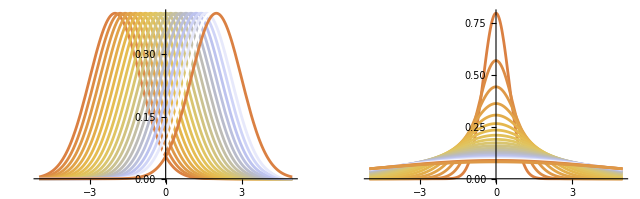

```mathematica
{Table[PDF[NormalDistribution[μ,1],x],{μ,-2,2,.2}]//Plot[#,{x,-5,5},PlotStyle->ResourceFunction["SampleColors"]["BeachColors",20]]&,Table[PDF[NormalDistribution[0,σ],x],{σ,.5,5,.2}]//Plot[#,{x,-5,5},PlotRange->All,PlotStyle->ResourceFunction["SampleColors"]["BeachColors",20]]&}//GraphicsRow
```

## CDF

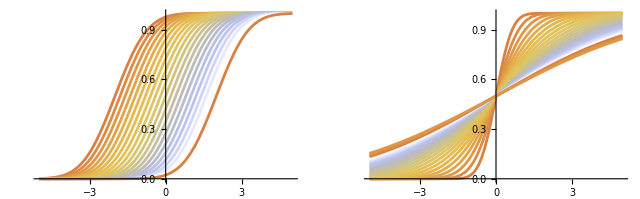

```mathematica
{Table[CDF[NormalDistribution[μ,1],x],{μ,-2,2,.2}]//Plot[#,{x,-5,5},PlotStyle->ResourceFunction["SampleColors"]["BeachColors",20]]&,Table[CDF[NormalDistribution[0,σ],x],{σ,.5,5,.2}]//Plot[#,{x,-5,5},PlotRange->All,PlotStyle->ResourceFunction["SampleColors"]["BeachColors",20]]&}//GraphicsRow
```

## PDF vs CDF

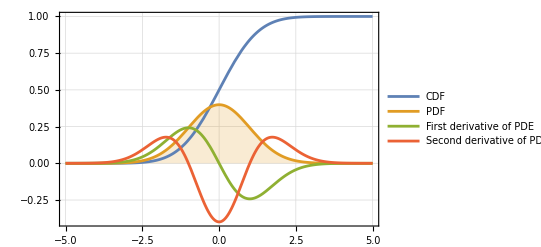

```mathematica
Plot[{CDF[NormalDistribution[],x],PDF[NormalDistribution[],x],Evaluate@D[PDF[NormalDistribution[],x],x],Evaluate@D[PDF[NormalDistribution[],x],x,x]},{x,-5,5},Filling->{2->Axis},PlotTheme->"Detailed",PlotLegends->Placed[{"CDF","PDF","First derivative of PDE","Second derivative of PDE"},{Left,Top}]]
```

## CDF vs PPF

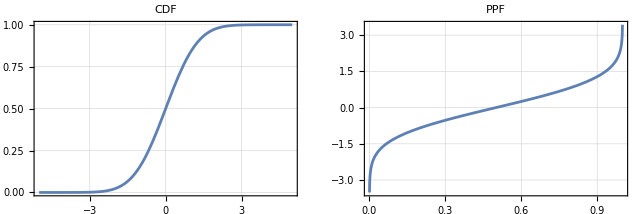

```mathematica
{Plot[CDF[NormalDistribution[],x],{x,-5,5},PlotTheme->"Detailed",PlotLabel->"CDF",PlotLegends->None],Plot[InverseCDF[NormalDistribution[],x],{x,0,1},PlotTheme->"Detailed",PlotLabel->"PPF",PlotLegends->None]}//GraphicsRow
```

## Z 分数

鸢尾花数据集

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"];
{sepalLength,sepalWidth,petalLength,petalWidth}=Table[irisData[[i,1,j]],{j,1,4},{i,1,150}];
```

数据标准化

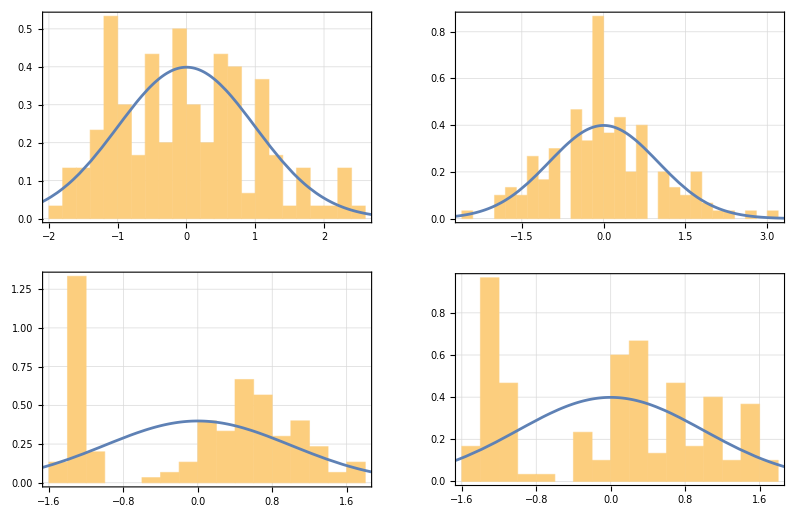

```mathematica
Show[Histogram[#,{0.2},"PDF",PlotTheme->"Detailed"],Plot[PDF[NormalDistribution[],x],{x,-4,4}]]&/@Standardize/@{sepalLength,sepalWidth,petalLength,petalWidth}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

## 68-95-99.7 法则

```mathematica
Probability[-#<x<#,x\[Distributed]NormalDistribution[]]&/@Range@3
```

{Erf[1/(√2)],Erf[√2],Erf[3/(√2)]}

```mathematica
NProbability[-#<x<#,x\[Distributed]NormalDistribution[]]&/@Range@3
```

{0.682689,0.9545,0.9973}

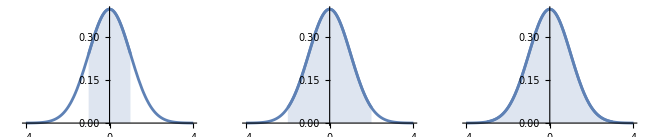

```mathematica
Show[Plot[PDF[NormalDistribution[],x],{x,-4,4}],#]&/@(Plot[PDF[NormalDistribution[],x],{x,-#,#},Filling->Axis,PlotRange->{0,.4}]&/@Range@3)//GraphicsRow
```

生成500个随机数

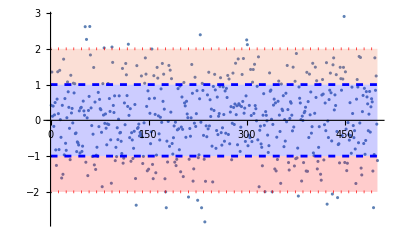

```mathematica
Show[ListPlot@Transpose@{Range@500,RandomVariate[NormalDistribution[],500]},Plot[{-1,1,-2,2},{x,0,500},PlotStyle->{{Blue,Dashed},{Blue,Dashed},{Red,Dotted},{Red,Dotted}},Filling->{1->{2},3->{1},4->{2}}]]
```

## 概率密度参数估计

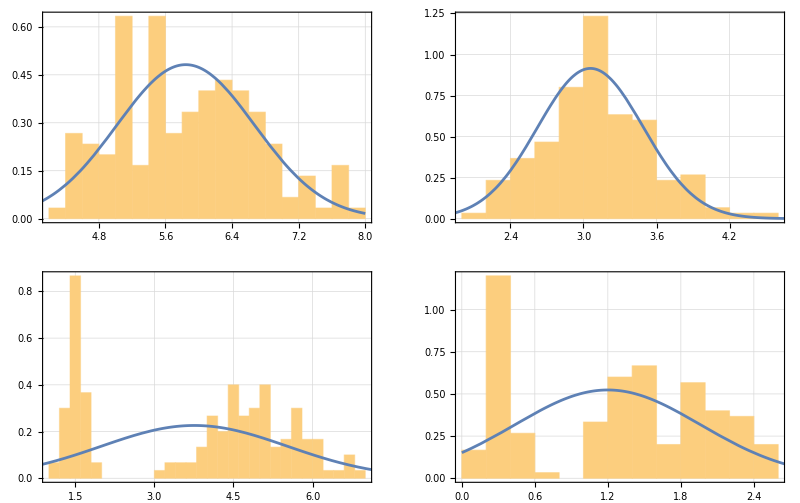

```mathematica
Show[Histogram[#,{.2},"PDF",PlotTheme->"Detailed"],Plot[PDF[NormalDistribution[Mean@#,StandardDeviation@#],x],{x,0,8},PlotRange->All]]&/@{sepalLength,sepalWidth,petalLength,petalWidth}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

## 经验分布函数

ECDF 和高斯 CDF

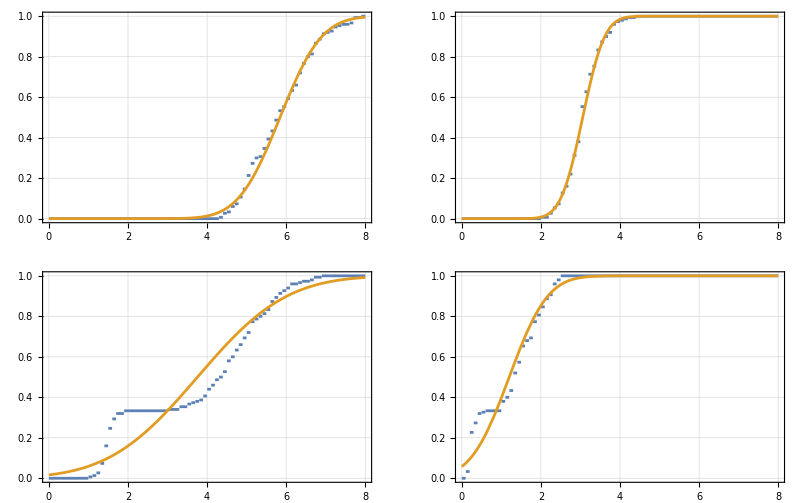

```mathematica
Plot[{CDF[EmpiricalDistribution@#,x],CDF[NormalDistribution[Mean@#,StandardDeviation@#],x]},{x,0,8},PlotTheme->"Detailed",PlotLegends->None]&/@{sepalLength,sepalWidth,petalLength,petalWidth}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

逆经验累积分布函数和高斯 PPF

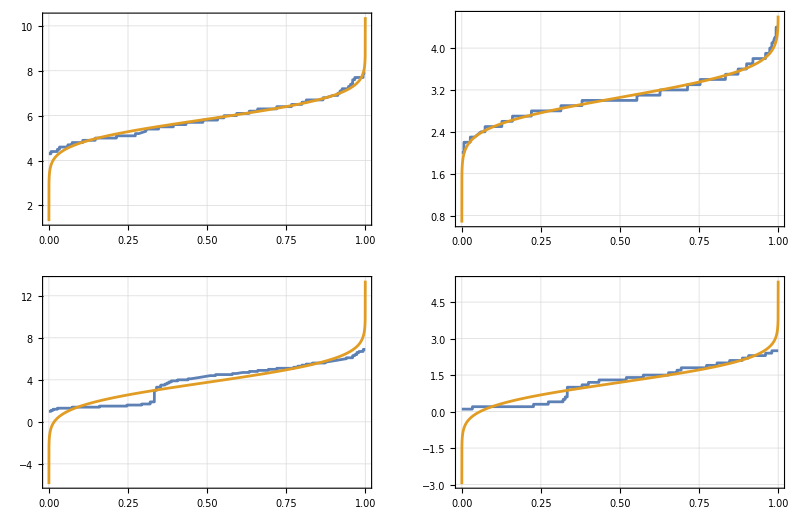

```mathematica
Plot[{Quantile[#,x],InverseCDF[NormalDistribution[Mean@#,StandardDeviation@#],x]},{x,0,1},PlotTheme->"Detailed",PlotLegends->None]&/@{sepalLength,sepalWidth,petalLength,petalWidth}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

## QQ 图

默认对比正态分布

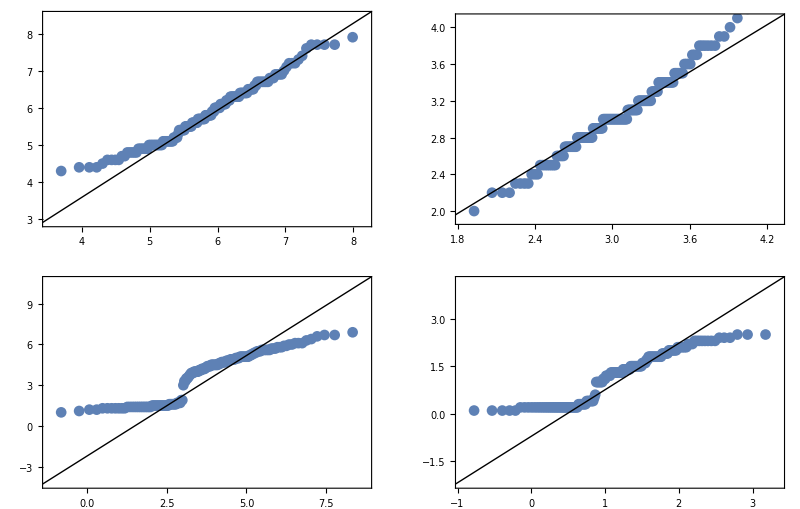

```mathematica
QuantilePlot[#,ReferenceLineStyle->Directive[Dashing[{}], Red](*设置参考线为红色实线*),PlotMarkers->Automatic]&/@{sepalLength,sepalWidth,petalLength,petalWidth}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

对比均匀分布

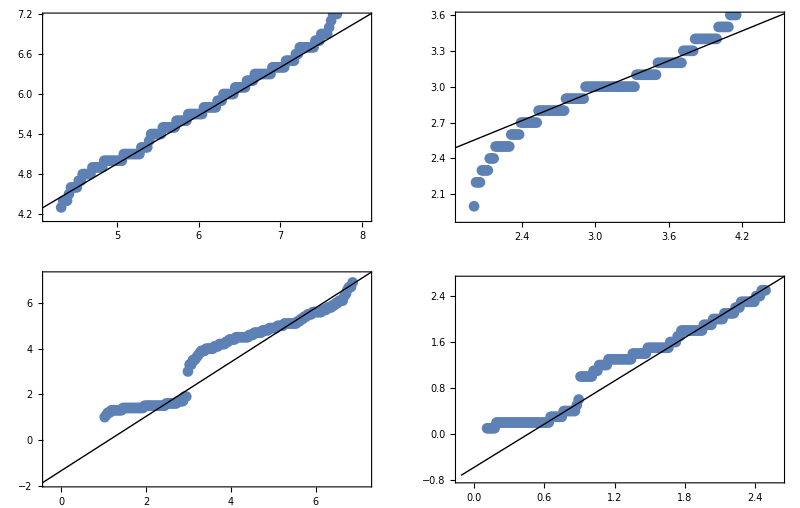

```mathematica
QuantilePlot[#,UniformDistribution[{a1,b1}],ReferenceLineStyle->Directive[Dashing[{}], Red],PlotMarkers->Automatic]&/@{sepalLength,sepalWidth,petalLength,petalWidth}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

## 二元高斯分布

## PDF曲面形状

```mathematica
surfaceMultinormalDistribution[fun_,σ1_,σ2_,ρ_]:=Plot3D[fun[MultinormalDistribution[{0,0},{{σ1^2,ρ σ1 σ2},{ρ σ1 σ2,σ2^2}}],{x,y}],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",PlotRange->All,PlotPoints->50,PlotTheme->"Minimal"]
```

```mathematica
surfaceMultinormalDistribution[#,1,2,.75]&/@{PDF,CDF}//GraphicsRow
```

-Graphics-

## 散点图

```mathematica
pointsMultinormalDistribution[σ1_,σ2_,ρ_]:=RandomVariate[MultinormalDistribution[{0,0},{{σ1^2,ρ σ1 σ2},{ρ σ1 σ2,σ2^2}}],8000]//ListPlot[#,PlotStyle->Black]&
```

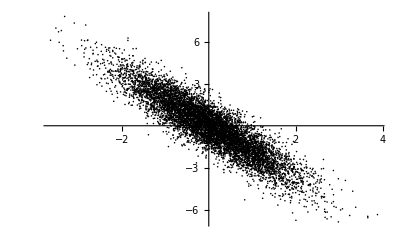
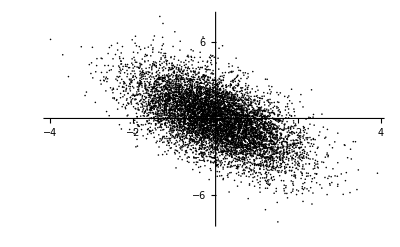
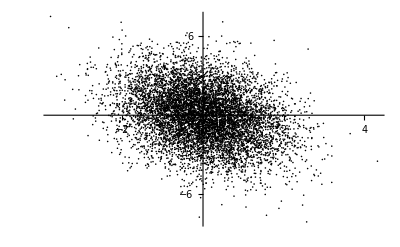
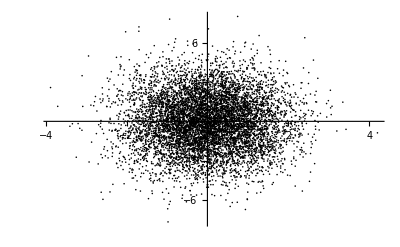
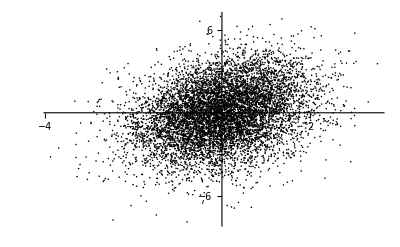
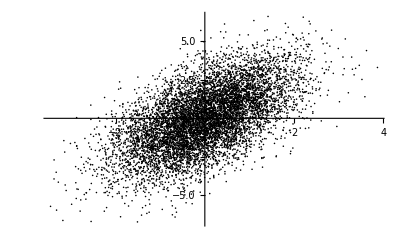
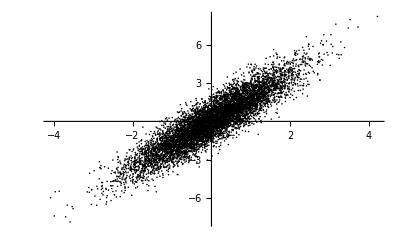

```mathematica
Table[pointsMultinormalDistribution[1,2,i],{i,-.9,.9,.3}]
```

## 安斯库姆四重奏

数据关系完全不同，但相关性系数几乎完全一致

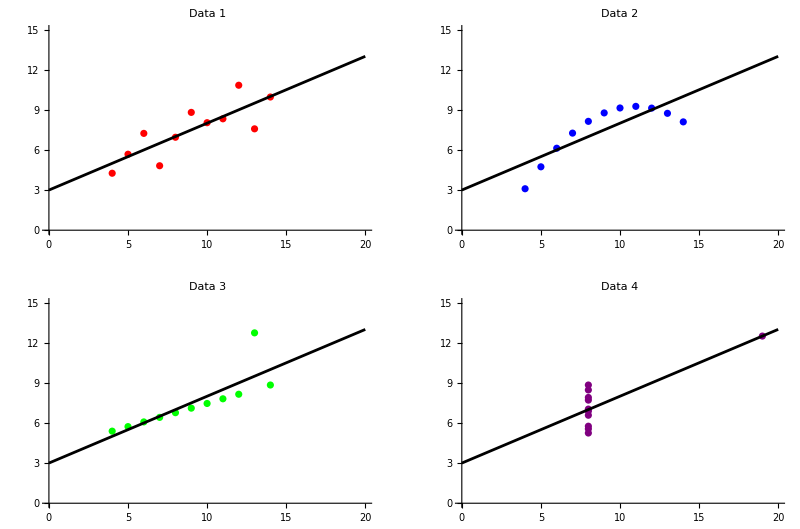

```mathematica
(*定义数据集*)
data1={{10,8.04},{8,6.95},{13,7.58},{9,8.81},{11,8.33},{14,9.96},{6,7.24},{4,4.26},{12,10.84},{7,4.82},{5,5.68}};
data2={{10,9.14},{8,8.14},{13,8.74},{9,8.77},{11,9.26},{14,8.1},{6,6.13},{4,3.1},{12,9.13},{7,7.26},{5,4.74}};
data3={{10,7.46},{8,6.77},{13,12.74},{9,7.11},{11,7.81},{14,8.84},{6,6.08},{4,5.39},{12,8.15},{7,6.42},{5,5.73}};
data4={{8,6.58},{8,5.76},{8,7.71},{8,8.84},{8,8.47},{8,7.04},{8,5.25},{19,12.5},{8,5.56},{8,7.91},{8,6.89}};
data={data1,data2,data3,data4};
colors={Red,Blue,Green,Purple};
labels={"Data 1","Data 2","Data 3","Data 4"};

(*定义绘图函数*)
plotWithFit[data_,color_,label_]:=Show[ListPlot[data,PlotStyle->color,PlotRange->{{0,20},{0,15}},PlotLabel->label],Plot[LinearModelFit[data,x,x]["BestFit"]//Normal//Evaluate,{x,0,20},PlotStyle->Black]]

(*生成带回归线的散点图网格*)
GraphicsGrid[Partition[MapThread[plotWithFit,{data,colors,labels}],2]]
```

## 相关性系数

对于鸢尾花数据集的花萼数据，总体线性相关系数小于零，然而分类计算的三个值显著大于零

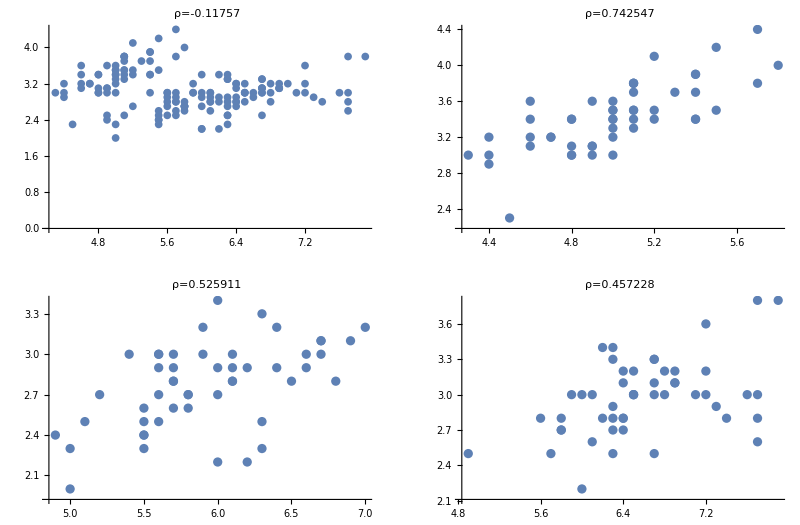

```mathematica
ListPlot[Transpose@#,PlotLabel->"ρ="<>ToString[Correlation@@#],PlotTheme->"Minimal"]&/@{{sepalLength,sepalWidth},{sepalLength[[1;;50]],sepalWidth[[1;;50]]},{sepalLength[[51;;100]],sepalWidth[[51;;100]]},{sepalLength[[101;;150]],sepalWidth[[101;;150]]}}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

## 平面等高线图

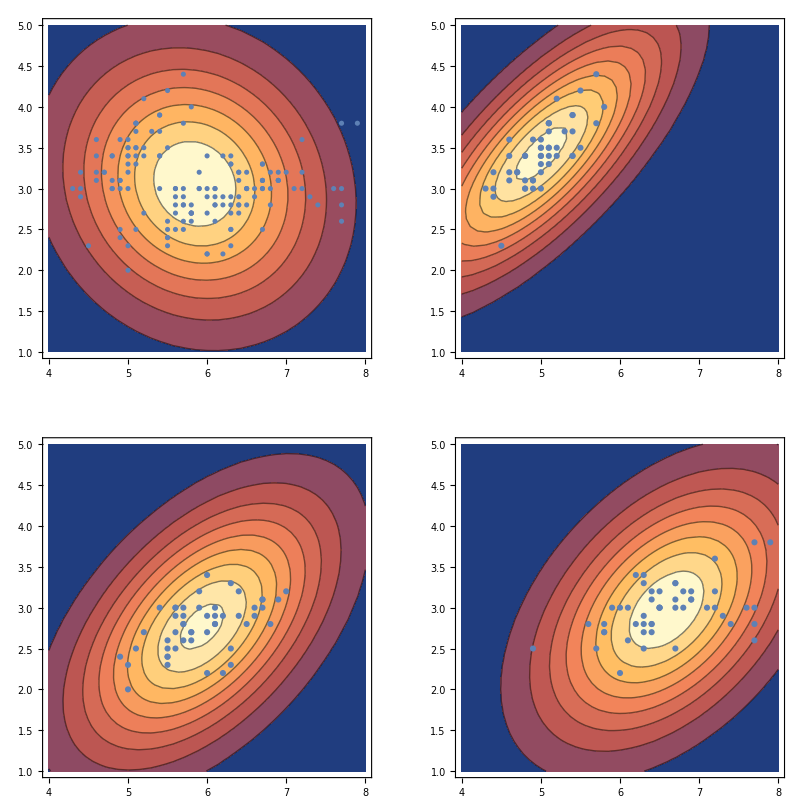

```mathematica
Show[ContourPlot[PDF[MultinormalDistribution[Mean/@#,Correlation@Transpose@#],{x,y}],{x,4,8},{y,1,5},PlotRange->All],ListPlot@Transpose@#]&/@{{sepalLength,sepalWidth},{sepalLength[[1;;50]],sepalWidth[[1;;50]]},{sepalLength[[51;;100]],sepalWidth[[51;;100]]},{sepalLength[[101;;150]],sepalWidth[[101;;150]]}}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

假设条件概率服从二元高斯分布，利用全概率定理，估算联合概率密度

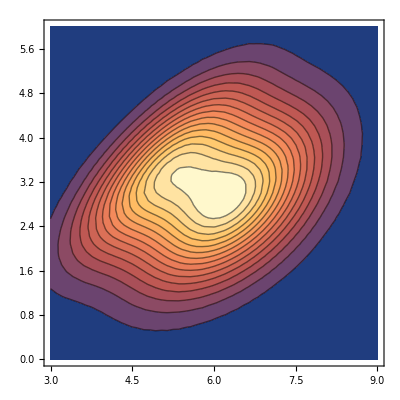

```mathematica
PDF[MultinormalDistribution[Mean/@#,Correlation@Transpose@#],{x,y}]&/@{{sepalLength[[1;;50]],sepalWidth[[1;;50]]},{sepalLength[[51;;100]],sepalWidth[[51;;100]]},{sepalLength[[101;;150]],sepalWidth[[101;;150]]}}//ContourPlot[Mean@#,{x,3,9},{y,0,6},PlotRange->All,Contours->15]&
```

## 多元高斯分布

## 三元高斯分布

自行绘制切片密度图

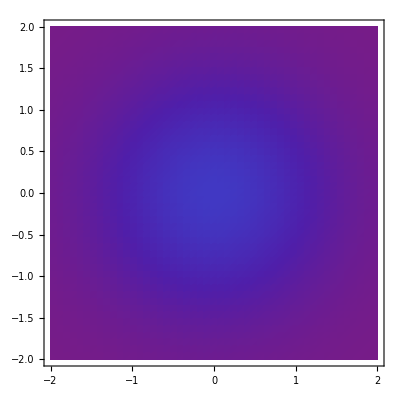
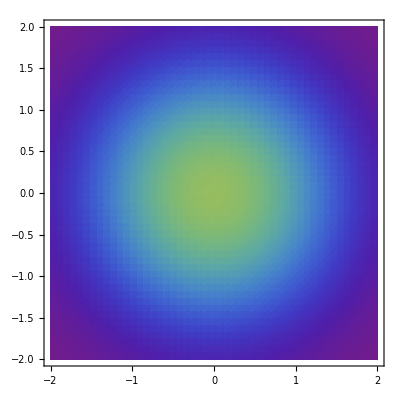
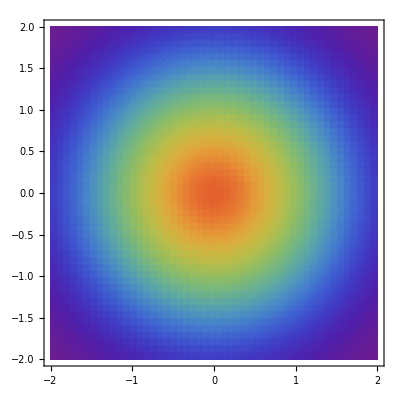
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[DensityPlot[PDF[MultinormalDistribution[{0,0,0},IdentityMatrix[3]],{x,y,z}],{x,-2,2},{y,-2,2},PlotPoints->50,PlotRange->{0,.07},ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,0.07}]]&),ColorFunctionScaling->False ],{z,-2,2} ]
```

切片密度图

```mathematica
SliceDensityPlot3D[PDF[MultinormalDistribution[{0,0,0},IdentityMatrix[3]],{x,y,z}],#,{x,-2,2},{y,-2,2},{z,-2,2},ColorFunction->"Rainbow",PlotTheme->"Minimal"]&/@{"CenterPlanes",{"ZStackedPlanes",5},"CenterCutSphere","CenterCutBox","DiagonalStackedPlanes"}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

切片等高线图

```mathematica
SliceContourPlot3D[PDF[MultinormalDistribution[{0,0,0},IdentityMatrix[3]],{x,y,z}],#,{x,-2,2},{y,-2,2},{z,-2,2},ColorFunction->"Rainbow",PlotTheme->"Minimal"]&/@{"CenterPlanes",{"ZStackedPlanes",5},"CenterCutSphere","CenterCutBox","DiagonalStackedPlanes"}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## 协方差矩阵

## 协方差矩阵和集中矩阵

协方差矩阵

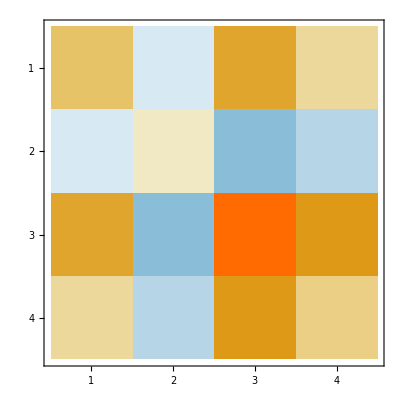
{(0.685694 | -0.042434 | 1.27432 | 0.516271
-0.042434 | 0.189979 | -0.329656 | -0.121639
1.27432 | -0.329656 | 3.11628 | 1.29561
0.516271 | -0.121639 | 1.29561 | 0.581006),-Graphics-}

```mathematica
{MatrixForm@#,MatrixPlot@#}&@Covariance@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}
```

集中矩阵（协方差矩阵的逆矩阵）

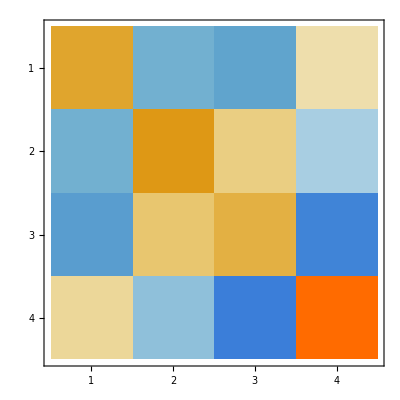
{(10.3147 | -6.71319 | -7.31448 | 5.73995
-6.71319 | 11.0584 | 6.48059 | -6.17093
-7.31448 | 6.48059 | 10.0317 | -14.5138
5.73995 | -6.17093 | -14.5138 | 27.6936),-Graphics-}

```mathematica
{MatrixForm@#,MatrixPlot@#}&@Inverse@Covariance@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}
```

给定标签为条件

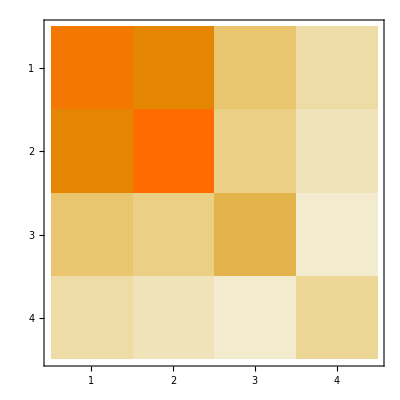
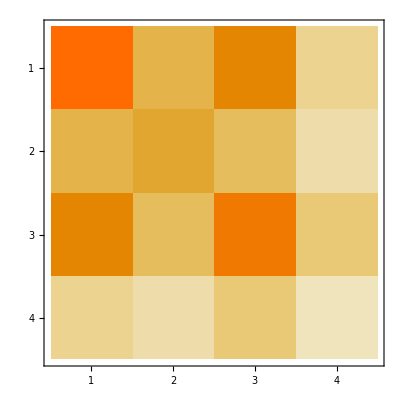
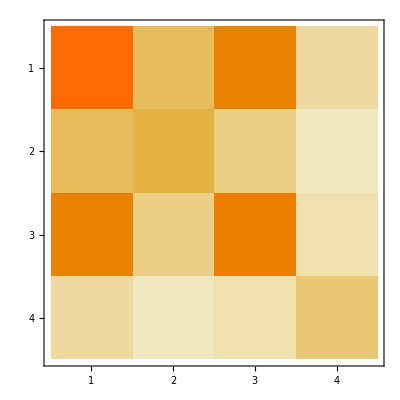

```mathematica
MatrixPlot@Covariance@Transpose@{sepalLength[[#]],sepalWidth[[#]],petalLength[[#]],petalWidth[[#]]}&/@{1;;50,51;;100,101;;150}
```

## 相关性系数矩阵

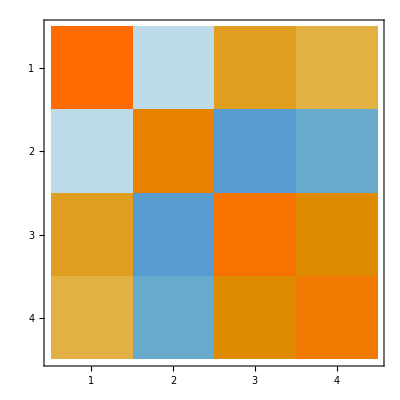
{(1. | -0.11757 | 0.871754 | 0.817941
-0.11757 | 1. | -0.42844 | -0.366126
0.871754 | -0.42844 | 1. | 0.962865
0.817941 | -0.366126 | 0.962865 | 1.),-Graphics-}

```mathematica
{MatrixForm@#,MatrixPlot@#}&@Correlation@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}
```

考虑标签

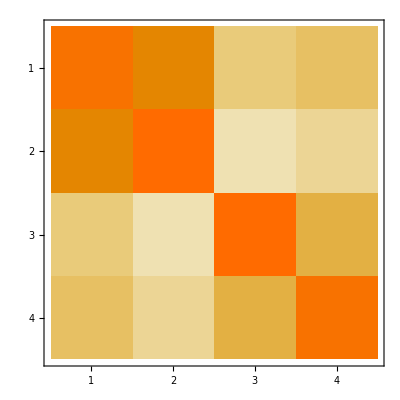
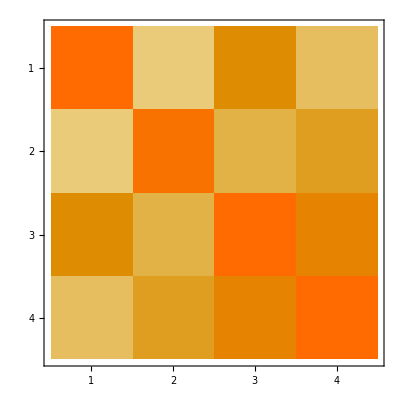
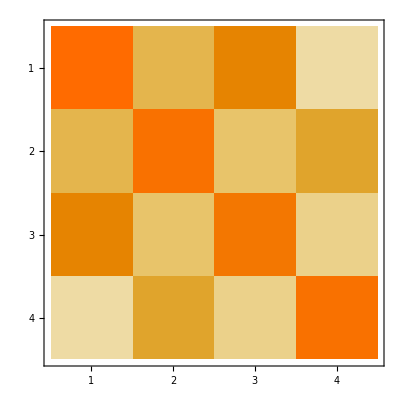

```mathematica
MatrixPlot@Correlation@Transpose@{sepalLength[[#]],sepalWidth[[#]],petalLength[[#]],petalWidth[[#]]}&/@{1;;50,51;;100,101;;150}
```

相关性系数矩阵和协方差矩阵的关系

```mathematica
DiagonalMatrix@StandardDeviation@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}.Correlation@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}.DiagonalMatrix@StandardDeviation@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}//MatrixForm
```

(0.685694 | -0.042434 | 1.27432 | 0.516271
-0.042434 | 0.189979 | -0.329656 | -0.121639
1.27432 | -0.329656 | 3.11628 | 1.29561
0.516271 | -0.121639 | 1.29561 | 0.581006)

## 特征值分解

```mathematica
covarMatrix=Covariance@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth};
correMatrix=Correlation@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth};
```

谱分解运算热图

```mathematica
String2Pic[string_]:=Rasterize[Text[string],RasterSize->100,ImageSize->150](*将符号转化为图片*)

SpectralMatrixPlot[matrix_]:=Module[{eig,plots},eig=Eigensystem@matrix;
plots={MatrixPlot[matrix,PlotTheme->"Minimal"],MatrixPlot[Rescale[eig[[1,#]] TensorProduct[eig[[2,#]],eig[[2,#]]](*谱分解为四项，决定特征向量重要性的是特征值大小*),MinMax@Flatten@matrix](*将矩阵归一化，方便热图显示矩阵值的大小*),PlotTheme->"Minimal"]&/@{1,2,3,4}};
GraphicsRow[{plots[[1]],String2Pic["≈"],plots[[2,1]],String2Pic["+"],plots[[2,2]],String2Pic["+"],plots[[2,3]],String2Pic["+"],plots[[2,4]]},ImageSize->600]]
```

```mathematica
SpectralMatrixPlot@covarMatrix
```

-Graphics-

```mathematica
SpectralMatrixPlot@correMatrix
```

-Graphics-

协方差矩阵的对角线

```mathematica
{PieChart[#,ChartLabels->{"X_1","X_2","X_3","X_4"}],BarChart[#,PlotTheme->"Detailed",BarOrigin->Left,ChartLabels->{"X_1","X_2","X_3","X_4"}]}&@Diagonal@covarMatrix//GraphicsRow
```

-Graphics-

## 欧氏距离 vs 马氏距离

质心坐标

```mathematica
meanVec=Mean/@{sepalLength,sepalWidth,petalLength,petalWidth}
```

{5.84333,3.05733,3.758,1.19933}

原点与质心的欧氏距离

```mathematica
EuclideanDistance[{0,0,0,0},meanVec]
```

7.68458

原点与质心的马氏距离

```mathematica
Sqrt[meanVec.Inverse@covarMatrix.Transpose@meanVec]
```

11.3686